X

(l Cos[q1[t]]
l Sin[q1[t]]
2 l Cos[q1[t]]
0
2 l Cos[q1[t]]+2 l Cos[q2[t]]
2 l Sin[q2[t]])

dX

(-l Sin[q1[t]] q1'[t]
l Cos[q1[t]] q1'[t]
-2 l Sin[q1[t]] q1'[t]
0
-2 l (Sin[q1[t]] q1'[t]+Sin[q2[t]] q2'[t])
2 l Cos[q2[t]] q2'[t])

m

(m1 | 0 | 0 | 0 | 0 | 0
0 | m1 | 0 | 0 | 0 | 0
0 | 0 | m2 | 0 | 0 | 0
0 | 0 | 0 | m2 | 0 | 0
0 | 0 | 0 | 0 | m3 | 0
0 | 0 | 0 | 0 | 0 | m3)

T

1/2 l^2 ((m1 Cos[q1[t]]^2+(m1+4 (m2+m3)) Sin[q1[t]]^2) q1'[t]^2+8 m3 Sin[q1[t]] Sin[q2[t]] q1'[t] q2'[t]+4 m3 (Cos[q2[t]]^2+Sin[q2[t]]^2) q2'[t]^2)

U

-g l m1 Sin[q1[t]]-2 g l m3 Sin[q2[t]]

L

g l m1 Sin[q1[t]]+2 g l m3 Sin[q2[t]]+1/2 l^2 ((m1 Cos[q1[t]]^2+(m1+4 (m2+m3)) Sin[q1[t]]^2) q1'[t]^2+8 m3 Sin[q1[t]] Sin[q2[t]] q1'[t] q2'[t]+4 m3 (Cos[q2[t]]^2+Sin[q2[t]]^2) q2'[t]^2)

dtdq1

1/2 l^2 (2 q1'[t] (-2 m1 Cos[q1[t]] Sin[q1[t]] q1'[t]+2 (m1+4 (m2+m3)) Cos[q1[t]] Sin[q1[t]] q1'[t])+8 m3 Cos[q1[t]] Sin[q2[t]] q1'[t] q2'[t]+8 m3 Cos[q2[t]] Sin[q1[t]] q2'[t]^2+2 (m1 Cos[q1[t]]^2+(m1+4 (m2+m3)) Sin[q1[t]]^2) q1''[t]+8 m3 Sin[q1[t]] Sin[q2[t]] q2''[t])

dtdq2

1/2 l^2 (8 m3 Cos[q1[t]] Sin[q2[t]] q1'[t]^2+8 m3 Cos[q2[t]] Sin[q1[t]] q1'[t] q2'[t]+8 m3 Sin[q1[t]] Sin[q2[t]] q1''[t]+8 m3 (Cos[q2[t]]^2+Sin[q2[t]]^2) q2''[t])

dq1

(2 (-2 g l m1 Sin[q1[t]]-4 g l m3 Sin[q2[t]]))/(l^2 (2 (m1+2 (m2+m3)-2 (m2+m3) Cos[2 q1[t]]) q1'[t]+8 m3 Sin[q1[t]] Sin[q2[t]] q2'[t]))

dq2

(-2 g l m1 Sin[q1[t]]-4 g l m3 Sin[q2[t]])/(4 l^2 m3 (Sin[q1[t]] Sin[q2[t]] q1'[t]+q2'[t]))

LangrageDiff1

l (-g m1 Cos[q1[t]]+2 l (m2+m3) Sin[2 q1[t]] q1'[t]^2+4 l m3 Cos[q2[t]] Sin[q1[t]] q2'[t]^2+l m1 Cos[q1[t]]^2 q1''[t]+l m1 Sin[q1[t]]^2 q1''[t]+4 l m2 Sin[q1[t]]^2 q1''[t]+4 l m3 Sin[q1[t]]^2 q1''[t]+4 l m3 Sin[q1[t]] Sin[q2[t]] q2''[t])

LangrageDiff2

2 l m3 (-g Cos[q2[t]]+2 l Cos[q1[t]] Sin[q2[t]] q1'[t]^2+2 l Sin[q1[t]] Sin[q2[t]] q1''[t]+2 l q2''[t])

H

-g l m1 Sin[q1[t]]-2 g l m3 Sin[q2[t]]+1/2 l^2 ((m1 Cos[q1[t]]^2+(m1+4 (m2+m3)) Sin[q1[t]]^2) q1'[t]^2+8 m3 Sin[q1[t]] Sin[q2[t]] q1'[t] q2'[t]+4 m3 (Cos[q2[t]]^2+Sin[q2[t]]^2) q2'[t]^2)

p1

1/2 l^2 (2 (m1+2 (m2+m3)-2 (m2+m3) Cos[2 q1[t]]) q1'[t]+8 m3 Sin[q1[t]] Sin[q2[t]] q2'[t])

p2

4 l^2 m3 (Sin[q1[t]] Sin[q2[t]] q1'[t]+q2'[t])

dp1

-l Cos[q1[t]] (-g m1+4 l (m2+m3) Sin[q1[t]] q1'[t]^2+4 l m3 Sin[q2[t]] q1'[t] q2'[t])

dp2

-2 l m3 Cos[q2[t]] (-g+2 l Sin[q1[t]] q1'[t] q2'[t])

dq1

(2 (-2 g l m1 Sin[q1[t]]-4 g l m3 Sin[q2[t]]))/(l^2 (2 (m1+2 (m2+m3)-2 (m2+m3) Cos[2 q1[t]]) q1'[t]+8 m3 Sin[q1[t]] Sin[q2[t]] q2'[t]))

dq2

(-2 g l m1 Sin[q1[t]]-4 g l m3 Sin[q2[t]])/(4 l^2 m3 (Sin[q1[t]] Sin[q2[t]] q1'[t]+q2'[t]))

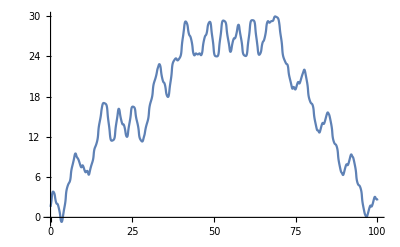

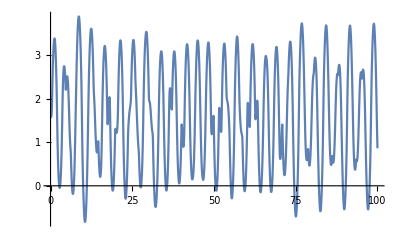

```mathematica
Clear["Global`*"];
(* Q - parameters Q = (q1 == alpha, q2 == beta) *)
(* Configuration *)
X := {
l*Cos[q1[t]],  (* x1 *)
l*Sin[q1[t]],  (* y1 *)
2*l*Cos[q1[t]], (* x2 *)
0 , (* y2 *)
(2*l*Cos[q1[t]]) + (2*l*Cos[q2[t]]), (* x3 == x2 + ... *)
0 + (2*l*Sin[q2[t]]) (* y3 == y2 + .... *)
};

dX := Simplify[D[X,t]];
m := ({{m1, 0, 0, 0, 0, 0}, {0, m1, 0, 0, 0, 0}, {0, 0, m2, 0, 0, 0}, {0, 0, 0, m2, 0, 0}, {0, 0, 0, 0, m3, 0}, {0, 0, 0, 0, 0, m3}});
G := {
0, 
-g, 
0, 
-g, 
 0, 
-g
};
(* Trig->False disabled trig. simplifications *)
T := Simplify[(m.dX.dX) / 2, Trig->False];
U := m.G.X;

(* Lagrange *)
L = T - U;
dtdq1 = D[D[L,q1'[t]],t];
dq1 = D[L,q1[t]];

dtdq2 = D[D[L,q2'[t]],t];
dq2 = D[L,q2[t]];

LangrageDiff1 = Simplify[dtdq1 - dq1];
LangrageDiff2 = Simplify[dtdq2 - dq2];

r1 = LangrageDiff1;
r2 = LangrageDiff2;

(* Hamilton *)
H = T + U;

p1 = Simplify[D[L, q1'[t]]];
p2 = Simplify[D[L, q2'[t]]];

dp1 = -Simplify[D[H, q1[t]]];
dp2 = -Simplify[D[H, q2[t]]];

(* H = pq' - L *)
dq1 = (H - L) / p1;
dq2 = (H - L) / p2;

(* Prints *)

Print["X"]
MatrixForm[X]

Print["dX"]
MatrixForm[dX]

Print["m"]
MatrixForm[m]

Print["T"]
MatrixForm[T]

Print["U"]
MatrixForm[U]

Print["L"]
MatrixForm[L]

Print["dtdq1"]
MatrixForm[dtdq1]
Print["dtdq2"]
MatrixForm[dtdq2]

Print["dq1"]
MatrixForm[dq1]
Print["dq2"]
MatrixForm[dq2]

Print["LangrageDiff1"]
MatrixForm[LangrageDiff1]

Print["LangrageDiff2"]
MatrixForm[LangrageDiff2]

Print["H"]
MatrixForm[H]

Print["p1"]
MatrixForm[p1]
Print["p2"]
MatrixForm[p2]

Print["dp1"]
MatrixForm[dp1]
Print["dp2"]
MatrixForm[dp2]

Print["dq1"]
MatrixForm[dq1]
Print["dq2"]
MatrixForm[dq2]

(* Example *)
m1 = 1;
m2 = 1;
m3 = 1;
g = 9.81;
l = 1;
T = 100;

sol=NDSolve[{
r1==0,r2==0,
q1[0]==Pi/2,q1'[0]==3,
q2[0]==Pi/2,q2'[0]==0
},
{q1,q2},{t,0,T}]; 

q1=First[q1/.sol];
q2=First[q2/.sol];

Plot[q1[t],{t,0,T}]
Plot[q2[t],{t,0,T}]


Animate[Graphics3D[{Line[{{-1.5,0,0},{1.5,0,0}}],Line[{{0,-1.5,0},{0,1.5,0}}],Line[{{0,0,-1.5},{0,0,1.5}}],Arrow[{{0,0,0},{
(2*l*Cos[q1[t]]) + (2*l*Cos[q2[t]]),
0 + (2*l*Sin[q2[t]]),
0}
}]}],{t,0,T}]
```